%%% DETERMIENS THE POSITION OF THE EVENT HORIZON, %%% for n = 4 of pc - GRm but arbitrary parameter value b : 
    %%% See Eqs. (30) and (31) of the manuscript.

```mathematica
f[y_]:=y^4-2 y^3+b/6
```

```mathematica
Solve[y^4-2 y^3+b/6==0,y]
```

{{y→1/2-(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3)))/(2 √3)-1/2 √(2-(2 b)/(3 (9 b+√(81 b^2-8 b^3))^(1/3))-1/3 (9 b+√(81 b^2-8 b^3))^(1/3)-(2 √3)/(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3))))},{y→1/2-(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3)))/(2 √3)+1/2 √(2-(2 b)/(3 (9 b+√(81 b^2-8 b^3))^(1/3))-1/3 (9 b+√(81 b^2-8 b^3))^(1/3)-(2 √3)/(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3))))},{y→1/2+(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3)))/(2 √3)-1/2 √(2-(2 b)/(3 (9 b+√(81 b^2-8 b^3))^(1/3))-1/3 (9 b+√(81 b^2-8 b^3))^(1/3)+(2 √3)/(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3))))},{y→1/2+(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3)))/(2 √3)+1/2 √(2-(2 b)/(3 (9 b+√(81 b^2-8 b^3))^(1/3))-1/3 (9 b+√(81 b^2-8 b^3))^(1/3)+(2 √3)/(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3))))}}

```mathematica
yi[b_]:=1/2-(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3)))/(2 √3)-1/2 √(2-(2 b)/(3 (9 b+√(81 b^2-8 b^3))^(1/3))-1/3 (9 b+√(81 b^2-8 b^3))^(1/3)-(2 √3)/(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3))))
```

```mathematica
yii[b_]:=1/2-(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3)))/(2 √3)+1/2 √(2-(2 b)/(3 (9 b+√(81 b^2-8 b^3))^(1/3))-1/3 (9 b+√(81 b^2-8 b^3))^(1/3)-(2 √3)/(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3))))
```

```mathematica
yiii[b_]:=1/2+(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3)))/(2 √3)-1/2 √(2-(2 b)/(3 (9 b+√(81 b^2-8 b^3))^(1/3))-1/3 (9 b+√(81 b^2-8 b^3))^(1/3)+(2 √3)/(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3))))
```

```mathematica
yiv[b_]:=1/2+(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3)))/(2 √3)+1/2 √(2-(2 b)/(3 (9 b+√(81 b^2-8 b^3))^(1/3))-1/3 (9 b+√(81 b^2-8 b^3))^(1/3)+(2 √3)/(√(3+(2 b)/((9 b+√(81 b^2-8 b^3))^(1/3))+(9 b+√(81 b^2-8 b^3))^(1/3))))
```

%%% Physical solution :

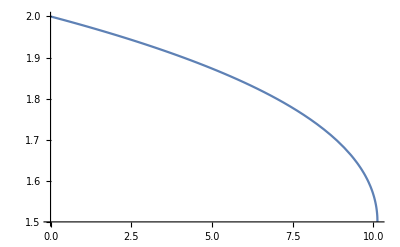

```mathematica
Plot[yiv[b],{b,0,81/8}]
```